## All definitions useful for the equations (Run this all)

## Metric and Chris symbols Definitions

```mathematica
quit[];
$Assumptions={r≥0,θ≥0,θ≤π,NN≥0,rh≥0,X≥0};
x={t,r,θ,φ};
gdd0={{-(1-2 M r/Σ[r,θ]), 0,0, -2 M r a X[θ]/Σ[r,θ] },{0,Σ[r,θ]/Δ[r],0,0},{0,0,Σ[r,θ],0},{-2 M r a X[θ]/Σ[r,θ],0,0,(r^2+a^2+2 M r a^2 X[θ]/Σ[r,θ])*X[θ]}}; 


(*rule1={Δ -> r^2+ a^2 -2 M r , Σ -> r^2+a^2Cos[θ]^2};*)
guu0=Inverse[gdd0];

guu1={{-(r^2+a^2+2M r a^2 X[θ]/Σ[r,θ])/Δ[r], 0,0, -2 M r a/(Σ[r,θ] Δ[r])},{0,Δ[r]/Σ[r,θ],0,0},{0,0,1/Σ[r,θ],0},{-2 M r a/(Σ[r,θ] Δ[r]),0,0,(Δ[r]-a^2X[θ])/(Σ[r,θ] Δ[r] X[θ])}};
Δ [r]:= r^2+ a^2 -2 M r ;
 Σ [r,θ]:= r^2+a^2Cos[θ]^2;
MatrixForm[gdd0];
MatrixForm[guu1];
X[θ_]:=Sin[θ]^2;
BISERIES[Z_]:=Z/.Union[{X'[θ]^2->4 X[θ](1-X[θ]),X''[θ]->2 (1-2X[θ])}];
```

```mathematica
dim=Length[gdd0];
Do[
Christ[i,j,k]=
Simplify[
BISERIES[Normal[Sum[1/2 guu0[[k]][[l]](D[gdd0[[l]][[i]],x[[j]]]+D[gdd0[[l]][[j]],x[[i]]]-D[gdd0[[j]][[i]],x[[l]]]),{l,1,dim}]]]];,{i,1,dim},{j,1,dim},{k,1,dim}];
Christ[3,2,3]
```

r/(a^2 cos^2(θ)+r^2)

The velocity definition

```mathematica
uu={-√(-1/gdd0[[1]][[1]]),0,0,0};
ud={1,0,0,0};
Do[ 
ud[[i]]=
Simplify[
Normal[
Sum[
gdd0[[i]][[j]]uu[[j]],{j,1, dim}]]];,
{i,1,dim}];
{ud[[1]],ud[[2]],ud[[3]],ud[[4]]};
Sum[uu[[i]]uu[[j]]gdd0[[i]][[j]], {i,1,dim}, {j,1,dim}]
FullSimplify[Sum[ud[[i]]ud[[j]]guu0[[i]][[j]], {i,1,dim}, {j,1,dim}]]
```

-1

-1

Lets compute down-index EM field and Maxwell tensor

```mathematica
Ad={0, Subscript[A, 2][t,r,θ, φ], Subscript[A, 3][t,r,θ, φ], Subscript[A, 4][t,r,θ, φ]};
Do[Adn[i]=Simplify[Normal[Ad[[i]],{ϵa,0,ORDERa}]],{i,1,dim}]
Do[FFdd[i,j]=Simplify[Normal[D[Adn[j],x[[i]]]-D[Adn[i],x[[j]]],{ϵa,0,ORDERa}]],{i,1,dim},{j,1,dim}];
FFdd[2,4]
huu={{0, 0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
hdd={{0, 0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
Do[
huu[[α]][[b]]=
Simplify[
Normal[
 guu0[[α]][[b]]+uu[[α]]uu[[b]]]],{α,1,dim}, {b,1,dim}]
Do[
hdd[[α]][[b]]=
Simplify[
Normal[
 gdd0[[α]][[b]]+ud[[α]]ud[[b]]]],{α,1,dim}, {b,1,dim}]
MatrixForm[huu]
```

A_4^(0,1,0,0)(t,r,θ,φ)-A_2^(0,0,0,1)(t,r,θ,φ)

((16 a^2 M^2 r^2 sin^2(θ))/((a^2+r (r-2 M)) (a^2 cos(2 θ)+a^2+2 r^2) (a^2 cos(2 θ)+a^2+2 r (r-2 M))) | 0 | 0 | -(4 a M r)/((a^2+r (r-2 M)) (a^2 cos(2 θ)+a^2+2 r^2))
0 | (a^2-2 M r+r^2)/(a^2 cos^2(θ)+r^2) | 0 | 0
0 | 0 | 1/(a^2 cos^2(θ)+r^2) | 0
-(4 a M r)/((a^2+r (r-2 M)) (a^2 cos(2 θ)+a^2+2 r^2)) | 0 | 0 | (2 csc^2(θ) (a^2 cos^2(θ)+r (r-2 M)))/((a^2+r (r-2 M)) (a^2 cos(2 θ)+a^2+2 r^2)))

N.B.!! Nelle somme, mettiamo α al posto di a sennò sostituisce il valore della somma (1, 2, 3, 4) nel parametro di rotazione della metrica!

And the upper ones!

```mathematica
Do[Aun[i]=FullSimplify[Sum[guu0[[i]][[j]]Adn[j],{j,1,dim}]],{i,1,dim}]
Do[FFuu[i,j]=Simplify[Normal[D[Aun[j],x[[i]]]-D[Aun[i],x[[j]]],{ϵa,0,ORDERa}]],{i,1,dim},{j,1,dim}];
Simplify[FFuu[2,4]+FFuu[4,2]]
```

0

finally, let' s compute FFdownup

```mathematica
Do[FFdu[i,j]=Sum[FFdd[i,k]guu0[[k]][[j]],{k,1,dim}],{i,1,dim},{j,1,dim}]
FFdu[2,4]
```

(((2 M r (a^2 cos^2(θ)+r^2))/(a^2-2 M r+r^2)-((a^2 cos^2(θ)+r^2)^2)/(a^2-2 M r+r^2)) (A_4^(0,1,0,0)(t,r,θ,φ)-A_2^(0,0,0,1)(t,r,θ,φ)))/(-(2 a^2 M r sin^4(θ) (a^2 cos^2(θ)+r^2))/(a^2-2 M r+r^2)-(a^2 sin^2(θ) (a^2 cos^2(θ)+r^2)^2)/(a^2-2 M r+r^2)-(r^2 sin^2(θ) (a^2 cos^2(θ)+r^2)^2)/(a^2-2 M r+r^2)+(2 a^2 M r sin^2(θ) (a^2 cos^2(θ)+r^2))/(a^2-2 M r+r^2)+(2 M r^3 sin^2(θ) (a^2 cos^2(θ)+r^2))/(a^2-2 M r+r^2))-(2 a M r sin^2(θ) (a^2 cos^2(θ)+r^2) A_2^(1,0,0,0)(t,r,θ,φ))/((a^2-2 M r+r^2) (-(2 a^2 M r sin^4(θ) (a^2 cos^2(θ)+r^2))/(a^2-2 M r+r^2)-(a^2 sin^2(θ) (a^2 cos^2(θ)+r^2)^2)/(a^2-2 M r+r^2)-(r^2 sin^2(θ) (a^2 cos^2(θ)+r^2)^2)/(a^2-2 M r+r^2)+(2 a^2 M r sin^2(θ) (a^2 cos^2(θ)+r^2))/(a^2-2 M r+r^2)+(2 M r^3 sin^2(θ) (a^2 cos^2(θ)+r^2))/(a^2-2 M r+r^2)))

## Covariant derivatives

let us define the covariant derivatives of vector objects

```mathematica
CovariantUp[i_,Funz_,j_]:=D[Funz[[j]],x[[i]]]+Sum[Christ[i,k,j]Funz[[k]],{k,1,4}](*∇_i A^j*)
CovariantDown[i_,Funz_,j_]:=D[Funz[[j]],x[[i]]]-Sum[Christ[i,j,k]Funz[[k]],{k,1,4}](*∇_i Subscript[A, j]*)
CovariantUpUp[i_,Funz_,j_,k_]:=D[Funz[j,k],x[[i]]]+Sum[Christ[α,i,j]Funz[α,k],{α,1,4}]+Sum[Christ[α,i,k]Funz[j,α],{α,1,4}](*∇_i A^jk*)
CovariantDownDown[i_,Funz_,j_,k_]:=D[Funz[j,k],x[[i]]]-Sum[Christ[i,j,α]Funz[α,k],{α,1,4}]-Sum[Christ[i,k,α]Funz[j,α],{α,1,4}](*∇_i Subscript[A, jk]*)
CovariantUp[1, uu, 3]
```

(2 a^2 M r sin(θ) cos(θ) √(-1/((2 M r)/(a^2 cos^2(θ)+r^2)-1)))/((a^2 cos^2(θ)+r^2)^3)

Same thing for tables

```mathematica
CovariantUpTable[i_,Funz_,j_]:=D[Funz[j],x[[i]]]+Sum[Christ[i,k,j]Funz[k],{k,1,4}](*∇_i A^j*)
CovariantDownTable[i_,Funz_,j_]:=D[Funz[j],x[[i]]]-Sum[Christ[i,j,k]Funz[k],{k,1,4}](*∇_i Subscript[A, j]*)
CovariantUpTable[1, Adn, 2]
```

(a M sin^2(θ) (a^2+r (r-2 M)) (a^2 cos^2(θ)-r^2) A_4(t,r,θ,φ))/((a^2 cos^2(θ)+r^2)^3)+A_2^(1,0,0,0)(t,r,θ,φ)

## Electric field

let' s compute E^a

```mathematica
Do[ElectricUp[i]=Sum[Subscript[m, e]/e *uu[[j]]CovariantUp[j,uu,i],{j,1,dim}],{i,1,dim}]
Simplify[ElectricUp[2]-Subscript[m, e]/e uu[[1]]^2Christ[1,1,2]]
```

0

now the down compoment E_a

```mathematica
Do[ElectricDown[i]=Sum[gdd0[[i]][[j]]ElectricUp[j],{j,1,dim}]//Simplify,{i,1,dim}]
Simplify[ElectricDown[2]-Subscript[m, e]/e uu[[1]]^2Christ[1,1,2]gdd0[[2]][[2]]]
ElectricDown[4]
```

0

0

## Vorticity and Deformation

Let's compute θ_ab and ω_ab with low indices (we shall call them  def and vort)by first defining v_ab. To do so, we need hdownup

```mathematica
hdu={{0, 0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
Do[hdu[[α]][[b]]=Sum[hdd[[α]][[c]]guu0[[c]][[b]],{c,1,dim}],{α,1,dim},{b,1,dim}]
Do[vdd[α,b]=Sum[hdu[[α]][[c]]hdu[[b]][[d]]CovariantDown[d,ud,c],{c,1,dim},{d,1,dim} ]//FullSimplify,{α,1,dim},{b,1,dim}]
```

```mathematica
Do[defdd[α,b]=1/2(vdd[α,b]+vdd[b,α])//FullSimplify,{α,1,dim}, {b,1,dim}]
Do[vortdd[α,b]=1/2(vdd[α,b]-vdd[b,α])//FullSimplify,{α,1,dim}, {b,1,dim}]
(*MatrixForm[Table[vortdd[α,b],{α,1,dim},{b,1,dim}]]
MatrixForm[Table[defdd[α,b],{α,1,dim},{b,1,dim}]]*)
```

In realtà a noi servono θ_a^b e ω_a^b, il primo chiaramente rimarrà 0. Nota che ω_a^b non è antisimmetrico

```mathematica
Do[vortdu[α,b]=Sum[vortdd[α,c]guu0[[c]][[b]],{c,1,dim}]//FullSimplify,{α,1,dim},{b,1,dim}]
Do[defdu[α,b]=Sum[defdd[α,c]guu0[[c]][[b]]//FullSimplify,{c,1,dim}],{α,1,dim},{b,1,dim}]
(*MatrixForm[Table[vortdu[α,b],{α,1,dim},{b,1,dim}]]
MatrixForm[Table[defdu[α,b],{α,1,dim},{b,1,dim}]]*)
```

```mathematica
Do[vortuu[α,b]=Sum[guu0[[α]][[c]]vortdu[c,b],{c,1,dim}]//Simplify,{α,1,dim},{b,1,dim}];
(*MatrixForm[Table[vortuu[α,b],{α,1,dim},{b,1,dim}]]*)
```

let' s check the vorticity tensor using the relation between vorticity and 4 velocity (eq . 2.22 first paper B e H)

```mathematica
Do[Checks[α,b]=Simplify[vortdd[α,b]-ud[[b]]Sum[uu[[c]]CovariantDown[c,ud,α],{c,1,dim}]-CovariantDown[b,ud,α]],{α,1,dim},{b,1,dim}]
Do[Checks2[α,b]=Simplify[vortdu[α,b]-uu[[b]]Sum[uu[[c]]CovariantDown[c,ud,α],{c,1,dim}]-Sum[guu0[[b]][[k]]CovariantDown[k,ud,α],{k,1,dim}]],{α,1,dim},{b,1,dim}]
(*MatrixForm[Table[Checks2[α,b],{α,1,dim},{b,1,dim}]]*)
```

```mathematica
MatrixForm[Table[Checks[α,b],{α,1,dim},{b,1,dim}]]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

ok, now we have all the ingredients to write the equation

## Magnetization

Consider un unmagnetised plasma means Fback_ij=0 with ij spatial indices. Indeed Fback_ij=ϵ_ijk B^k thus B^k=0. However we want to write our Larmor tensor as ω_a^b, meaning we need B_a^b which is not always 0. For example Fback_r^φ=Fback_r0 g^(0φ) which is different from 0. Therefore let us construct the whole Fback tensor

```mathematica
Do[Fback[k,j]=0,{k,1,dim},{j,1,dim}];
Do[Fback[α,1]=Subscript[m, e]/e  CovariantDown[1,ud,α]//Simplify,{α,1,4}]
Do[Fback[1,α]=- Fback[α, 1], {α, 1, dim}];
MatrixForm[Table[Fback[α,b],{α,1,dim},{b,1,dim}]];
```

```mathematica
Do[Larmordd[α,b]=-e/Subscript[m, e]Sum[hdu[[α]][[j]]hdu[[b]][[k]]Fback[j,k],{j,1,dim},{k,1,dim}]//FullSimplify,{α,1,dim},{b,1,dim}]
MatrixForm[Table[Larmordd[α,b],{α,1,dim},{b,1,dim}]];
```

```mathematica
Do[
Larmordu[α,b]=Sum[Larmordd[α,k]guu0[[k]][[b]],{k,1,dim}]//FullSimplify,{α,1,dim},{b,1,dim}];
MatrixForm[Table[Larmordu[α,b],{α,1,dim},{b,1,dim}]];
```

```mathematica
Breuer Equations
```

Breuer Equations

Null

## Now the final equations

## General equation

```mathematica
Do[
DerivativeFF[i]=Sum[ guu0[[b]][[j]]CovariantDownDown[j,FFdd,i,b],{b,1,dim},{j,1,dim}]//Simplify,{i,1,dim}
]
Speak["Finito"]
```

THe various pieces of the equation

```mathematica
Do[
Firstterm[i]=Sum[hdu[[i]][[k]]uu[[1]]CovariantDownTable[1, DerivativeFF, k],{k,1,dim}],{i,1,dim}
];
Do[
Secondterm[i]= Sum[vortdu[i,k]DerivativeFF[k],{k,1,dim}]//Simplify,{i,1,dim}
];
Do[Thirdterm[i]=Sum[(e/Subscript[m, e] ElectricDown[i]uu[[j]]+Larmordu[i,j])DerivativeFF[j],{j,1,dim}],{i,1,dim}]
Thirdterm[2];
Do[
Fourthterm[i]=-Subscript[ω, p]^2(Sum[FFdd[i,j]uu[[j]],{j,1,dim}])
,{i,1,dim}
];
Speak["Finito"]
```

Now the final BH equation

```mathematica
Do[Breuereq[i]=(Firstterm[i]+Secondterm[i]+Thirdterm[i]+Fourthterm[i]), {i,1,dim}];
Speak["Finito"]
```

## Slow rotation approximation

```mathematica
Do[BreuereqSR[i]=Series[Breuereq[i],{a,0,1}]//Simplify,{i,1,dim}];
Speak["Finito"]
```

## Now we will expand in spherical harmonics and study the various components of the equations

## Multipolar expansion

Multipolar Expansion in spherical harmonics

```mathematica
ansatzangular={Subscript[A, 2]->Function [{t,r,θ,φ},hh[r,t]Y[θ,φ]],Subscript[A, 3]->Function [{t,r,θ,φ},vv[r,t]/Sin[θ] D[Y[θ,φ],φ]+kk[r,t]D[Y[θ,φ],θ]],Subscript[A, 4]->Function [{t,r,θ,φ},kk[r,t]D[Y[θ,φ],φ]-vv[r,t]Sin[θ]D[Y[θ,φ],θ]]};
```

Rules for Spherical Harmonics

```mathematica
$Assumptions={r≥0,θ≥0,θ≤π};
Sθ[θ_,φ_]:=-1/Sin[θ] D[Y[θ,φ],φ];
Sφ[θ_,φ_]:=Sin[θ]D[Y[θ,φ],θ];
X[θ_]:=Sin[θ]^2;
ruleANG={Derivative[2,0][Y][θ,φ]->-l(l+1)Y[θ,φ]-1/Sin[θ]^2 Derivative[0,2][Y][θ,φ]-Cot[θ]Derivative[1,0][Y][θ,φ],Derivative[3,0][Y][θ,φ]->l (1+l) Cot[θ] Y[θ,φ]-(1+l+l^2) Derivative[1,0][Y][θ,φ]+Csc[θ]^2 (3 Cot[θ] Derivative[0,2][Y][θ,φ]+2 Derivative[1,0][Y][θ,φ]-Derivative[1,2][Y][θ,φ]),Derivative[4,0][Y][θ,φ]->l (1+l) (1+l+l^2-3 Csc[θ]^2) Y[θ,φ]+Csc[θ] (Csc[θ] (7+l+l^2-11 Csc[θ]^2) Derivative[0,2][Y][θ,φ]+((1+2 l (1+l)) Cos[θ]-6 Cot[θ] Csc[θ]) Derivative[1,0][Y][θ,φ]+Csc[θ] (5 Cot[θ] Derivative[1,2][Y][θ,φ]-Derivative[2,2][Y][θ,φ])),Derivative[2,1][Y][θ,φ]->-l (1+l) Derivative[0,1][Y][θ,φ]-Csc[θ]^2 Derivative[0,3][Y][θ,φ]-Cot[θ] Derivative[1,1][Y][θ,φ],Derivative[2,2][Y][θ,φ]->-l (1+l) Derivative[0,2][Y][θ,φ]-Csc[θ]^2 Derivative[0,4][Y][θ,φ]-Cot[θ] Derivative[1,2][Y][θ,φ]};
ruleANG2={Derivative[1,1][Y][θ,φ]->1/2 XX[θ,φ]+Cot[θ] Derivative[0,1][Y][θ,φ],Derivative[0,2][Y][θ,φ]->-1/2 Sin[θ] (Sin[θ] (W[θ,φ]+l (1+l) Y[θ,φ])+2 Cos[θ] Derivative[1,0][Y][θ,φ]),Derivative[2,0][Y][θ,φ]->1/2 (W[θ,φ]-l (1+l) Y[θ,φ]),Derivative[3,0][Y][θ,φ]->1/2 (-3 Cot[θ] W[θ,φ]-l (1+l) Cot[θ] Y[θ,φ]-2 (-2+l+l^2+Csc[θ]^2) Derivative[1,0][Y][θ,φ]-2 Csc[θ]^2 Derivative[1,2][Y][θ,φ]),Derivative[4,0][Y][θ,φ]->1/2 (-(7+2 l (1+l)-11 Csc[θ]^2) W[θ,φ]+2 Csc[θ]^4 Derivative[0,4][Y][θ,φ]+Cot[θ] (5 l (1+l) Cot[θ] Y[θ,φ]+2 (-6+5 Csc[θ]^2) Derivative[1,0][Y][θ,φ]+12 Csc[θ]^2 Derivative[1,2][Y][θ,φ])),Derivative[2,1][Y][θ,φ]->-1/2 Cot[θ] XX[θ,φ]-(l+l^2+Cot[θ]^2) Derivative[0,1][Y][θ,φ]-Csc[θ]^2 Derivative[0,3][Y][θ,φ],Derivative[2,2][Y][θ,φ]->-Csc[θ]^2 Derivative[0,4][Y][θ,φ]+1/2 l (1+l) Sin[θ] (Sin[θ] (W[θ,φ]+l (1+l) Y[θ,φ])+2 Cos[θ] Derivative[1,0][Y][θ,φ])-Cot[θ] Derivative[1,2][Y][θ,φ],Derivative[3,1][Y][θ,φ]->1/4 (-2 (1+l+l^2-2 Csc[θ]^2) XX[θ,φ]+Csc[θ]^3 ((7 Cos[θ]+Cos[3 θ]) Derivative[0,1][Y][θ,φ]+12 Cos[θ] Derivative[0,3][Y][θ,φ]-4 Sin[θ] Derivative[1,3][Y][θ,φ]))};
```

```mathematica
ruleNOφ={Derivative[0,1][Y][θ,φ]->I m Y[θ,φ],Derivative[0,2][Y][θ,φ]->-m^2 Y[θ,φ],Derivative[1,1][Y][θ,φ]->I m Derivative[1,0][Y][θ,φ],Derivative[1,2][Y][θ,φ]->-m^2 Derivative[1,0][Y][θ,φ],Derivative[0,3][Y][θ,φ]->-I m^3 Y[θ,φ]};
ruleT=Union[ruleANG,ruleNOφ,{√(Sin[θ]^2)->Sin[θ]}];
```

```mathematica
ruleFinal=Union[ansatzangular, ruleT];
```

## The various components with the multipolar expansion

### Let’s start with the radial component of the equation

```mathematica
BHr=BreuereqSR[2]//.{ruleFinal}//Simplify
```

{-(1/(r (r-2 M)))^(3/2) Y(θ,φ) (hh^(0,3)(r,t) r^3-(2 M-r) (l^2+l+r^2 ω_p^2) hh^(0,1)(r,t)+l (l+1) (2 M-r) kk^(1,1)(r,t))+1/r^(11/2)2 ⅈ M (1/(r-2 M))^(5/2) (2 m M (2 M^2-3 r M+r^2) hh(r,t) Y(θ,φ)+m (2 (2 M-r) hh^(0,2)(r,t) r^4+(r-M) kk^(0,2)(r,t) r^3-(2 M-r) (kk^(1,2)(r,t) r^4+(2 M^2-3 r M+r^2) hh^(1,0)(r,t) r-(2 M^2-3 r M+r^2) kk^(2,0)(r,t) r+2 M (M-r) kk^(1,0)(r,t))) Y(θ,φ)+ⅈ sin(θ) Y^(1,0)(θ,φ) ((r-M) vv^(0,2)(r,t) r^3+l (l+1) (2 M^2-3 r M+r^2) vv(r,t)+(2 M-r) (-vv^(1,2)(r,t) r^4+(2 M^2-3 r M+r^2) vv^(2,0)(r,t) r-2 M (M-r) vv^(1,0)(r,t)))) a+O(a^2)}

Now, here we take a look at Paolo’s notes on Perturbation Theory to see how this equation is looking like. We take the equation 99, which is the polar part of the Einstein equation and we are only interested of course to the vectorial component 

δE_r=(A_l+(A^∼)_l cosθ) Y^l+B_l sinθ (Y^l)_(,θ)+C_l (Y^l)_(,ϕ) 

but notice that  (Y^l)_(,ϕ) is just  im ϕ(Y^l)

```mathematica
CoeffYl1=Simplify[Coefficient[BHr,Y[θ,φ]]];
```

```mathematica
AlCl=Simplify[Coefficient[CoeffYl1,Cos[θ],0]](* This is the coefficient of Y^l, namely Subscript[A, l]+im Subscript[C, l]*);
Altilde=Simplify[Coefficient[CoeffYl1,Cos[θ],1]](* This is the coefficient of cosθ Y^l, namely Subscript[A, l] tilde*);
```

```mathematica
AlCl Y[θ,φ]+Altilde Cos[θ]Y[θ,φ]-CoeffYl1 Y[θ,φ]//Simplify
```

{0}

```mathematica
DerTheta=Simplify[Coefficient[BHr,Derivative[1,0][Y][θ,φ]]];(*This is the piece with the derivative (Y^l)_(,θ)*)
Bl=Simplify[Coefficient[DerTheta,Sin[θ],1]];(*And this is the corresponding coefficiend Subscript[B, l]*)
```

Let’s verify that indeed this separation is good

```mathematica
Normal[Simplify[Sin[θ]Bl Derivative[1,0][Y][θ,φ]+Altilde Cos[θ]Y[θ,φ]+AlCl Y[θ,φ]-BHr]](* Ok *)
```

{0}

### Now let’s go to the θ part of the equation

```mathematica
BHtheta=BreuereqSR[3]//.{ruleFinal}//Simplify;
```

```mathematica
BHthetasimpli=FullSimplify[BHtheta/.Cos[2θ]->1-2 Sin[θ]^2]
```

{(1/(r (r-2 M)))^(3/2) (ⅈ m csc(θ) Y(θ,φ) (-vv^(0,3)(r,t) r^3+(2 M-r) (l^2+l+r^2 ω_p^2) vv^(0,1)(r,t)+(2 M-r) ((2 M-r) r vv^(2,1)(r,t)-2 M vv^(1,1)(r,t)))-Y^(1,0)(θ,φ) (kk^(0,3)(r,t) r^3+hh^(1,1)(r,t) r^3+(r-2 M) ω_p^2 kk^(0,1)(r,t) r^2-4 M hh^(1,1)(r,t) r^2+4 M^2 hh^(1,1)(r,t) r-2 M kk^(1,1)(r,t) r-(r-2 M)^2 kk^(2,1)(r,t) r+2 M (r-2 M) hh^(0,1)(r,t)+4 M^2 kk^(1,1)(r,t)))-1/r^(9/2)2 (M (1/(r-2 M))^(3/2) sin(θ) (-4 ⅈ m M (2 M-r) cot(θ) csc(θ) hh(r,t) Y(θ,φ)-(-2 ⅈ m cot(θ) csc(θ) kk^(0,2)(r,t) r^3+(l^2+l+m^2 csc^2(θ)) vv^(0,2)(r,t) r^3-2 ⅈ m (2 M-r) cot(θ) csc(θ) ((2 M-r) r hh^(1,0)(r,t)+2 M kk^(1,0)(r,t)+r (r-2 M) kk^(2,0)(r,t))) Y(θ,φ)+csc(θ) Y^(1,0)(θ,φ) (ⅈ m kk^(0,2)(r,t) r^3+2 l (l+1) (2 M-r) cos(θ) vv(r,t)+2 cos(θ) ((2 M-r) ((2 M-r) r vv^(2,0)(r,t)-2 M vv^(1,0)(r,t))-r^3 vv^(0,2)(r,t))))) a+O(a^2)}

This should be compared with Eq. 100 of Paolo’s Lectures, where we keep as before only the terms up to order one in the rotation parameter and only the vector part of course

δE_θ=(α_l+(α^∼)_l cosθ) (Y^l)_(,θ)-(β_l+(β^∼)_l tilde cosθ) ((Y^l)_(,ϕ))/sinθ+η_l sinθ Y^l

```mathematica
Coef=Simplify[Coefficient[(1/Sin[θ])^0 BHthetasimpli,Y[θ,φ]]](* Coefficient of Y^l*)
```

{1/r^(9/2)ⅈ csc(θ) (1/(r-2 M))^(3/2) (-16 a m M^3 r cos(θ) hh^(1,0)(r,t)+16 a m M^2 r^2 cos(θ) hh^(1,0)(r,t)-4 a m M r^3 cos(θ) hh^(1,0)(r,t)+8 a m M^2 cos(θ) (2 M-r) hh(r,t)+16 a m M^3 r cos(θ) kk^(2,0)(r,t)-16 a m M^3 cos(θ) kk^(1,0)(r,t)-16 a m M^2 r^2 cos(θ) kk^(2,0)(r,t)+8 a m M^2 r cos(θ) kk^(1,0)(r,t)-4 a m M r^3 cos(θ) kk^(0,2)(r,t)+4 a m M r^3 cos(θ) kk^(2,0)(r,t)-2 ⅈ a l^2 M r^3 sin^2(θ) vv^(0,2)(r,t)-2 ⅈ a l M r^3 sin^2(θ) vv^(0,2)(r,t)-2 ⅈ a m^2 M r^3 vv^(0,2)(r,t)+m r^3 (2 M-r) vv^(0,1)(r,t) (l^2+l+r^2 ω_p^2)+4 m M^2 r^4 vv^(2,1)(r,t)-4 m M^2 r^3 vv^(1,1)(r,t)-4 m M r^5 vv^(2,1)(r,t)+2 m M r^4 vv^(1,1)(r,t)-m r^6 vv^(0,3)(r,t)+m r^6 vv^(2,1)(r,t))}

```mathematica
betal=-Simplify[Coefficient[Coefficient[Coefficient[Coef,Csc[θ],1]/(I m),Cos[θ],0],Sin[θ]^2,0]](*The 1/(I m) comes from the fact that in Paolo's definition the coefficients comes from the term with the derivative respect to ϕ, while we were writing it in terms of Y^l(which brings down a I m )*)
betatildel=-Simplify[Coefficient[Coefficient[Coef,Csc[θ],1]/(I m),Cos[θ],1]]
etal=Simplify[Coefficient[Coefficient[Coef, Csc[θ],1], Sin[θ]^2, 1]](*Simplify[Coefficient[Coefficient[Coef,Csc[θ],0],Sin[θ],1]];*)
```

{-(1/(r (r-2 M)))^(3/2) (-2 ⅈ a m M vv^(0,2)(r,t)+(2 M-r) vv^(0,1)(r,t) (l^2+l+r^2 ω_p^2)+4 M^2 r vv^(2,1)(r,t)-4 M^2 vv^(1,1)(r,t)-4 M r^2 vv^(2,1)(r,t)+2 M r vv^(1,1)(r,t)+r^3 (-vv^(0,3)(r,t))+r^3 vv^(2,1)(r,t))}

{(4 a M (1/(r-2 M))^(3/2) ((2 M-r) (r (2 M-r) hh^(1,0)(r,t)+2 M kk^(1,0)(r,t)+r (r-2 M) kk^(2,0)(r,t))+2 M (r-2 M) hh(r,t)+r^3 kk^(0,2)(r,t)))/r^(9/2)}

{2 a l (l+1) M (1/(r (r-2 M)))^(3/2) vv^(0,2)(r,t)}

```mathematica
Sin[θ]^2 Csc[θ]etal-I m betatildel Csc[θ]Cos[θ]-I m betal Csc[θ]-Coef//FullSimplify
```

{0}

```mathematica
DerTheta2=Simplify[Coefficient[BHthetasimpli,Derivative[1,0][Y][θ,φ]]](*This is the piece with the derivative (Y^l)_(,θ)*)
```

{-1/r^(9/2)(1/(r-2 M))^(3/2) (2 ⅈ a m M r^3 kk^(0,2)(r,t)+4 a l (l+1) M cos(θ) (2 M-r) vv(r,t)+16 a M^3 r cos(θ) vv^(2,0)(r,t)-16 a M^3 cos(θ) vv^(1,0)(r,t)-16 a M^2 r^2 cos(θ) vv^(2,0)(r,t)+8 a M^2 r cos(θ) vv^(1,0)(r,t)-4 a M r^3 cos(θ) vv^(0,2)(r,t)+4 a M r^3 cos(θ) vv^(2,0)(r,t)+4 M^2 r^4 hh^(1,1)(r,t)-4 M r^5 hh^(1,1)(r,t)+2 M r^3 (r-2 M) hh^(0,1)(r,t)+r^6 hh^(1,1)(r,t)-4 M^2 r^4 kk^(2,1)(r,t)+4 M^2 r^3 kk^(1,1)(r,t)-2 M r^5 ω_p^2 kk^(0,1)(r,t)+4 M r^5 kk^(2,1)(r,t)-2 M r^4 kk^(1,1)(r,t)+r^6 ω_p^2 kk^(0,1)(r,t)+r^6 kk^(0,3)(r,t)-r^6 kk^(2,1)(r,t))}

```mathematica
alfa=Simplify[Coefficient[DerTheta2,Cos[θ],0]];
alfatilde=Simplify[Coefficient[DerTheta2,Cos[θ],1]];
```

Let’s verify that indeed this separation is good

```mathematica
Normal[Simplify[(alfa+alfatilde Cos[θ])Derivative[1,0][Y][θ,φ]-(betal+betatildel Cos[θ])I m Y[θ,φ]Csc[θ]+etal Y[θ,φ] Sin[θ]-BHthetasimpli]](* Ok *)
```

{0}

### Now let’s go to the ϕ part of the equation

```mathematica
BHphi=BreuereqSR[4]*Csc[θ]//.{ruleFinal}//Simplify;
```

This should be compared with Eq. 101 of Paolo’s Lectures, where we keep as before only the terms up to order one in the rotation parameter and only the vector part of course

δE_θ=(β_l+(β^∼)_l cosθ) (Y^l)_(,θ)+(α_l+(α^∼)_l cosθ) ((Y^l)_(,ϕ))/sinθ+ζ_l sinθ Y^l 

and we see that the coefficient of the first term, are the same of the coefficient of the ((Y^l)_(,ϕ))/sinθ term in the θ-equation and the coefficients of the ((Y^l)_(,ϕ))/sinθ term (second term here) are the same of the coeffienct of (Y^l)_(,θ) in the θ-equation. Let’s verify it calling the parameters differently

```mathematica
Coef2=Simplify[Coefficient[BHphi,Y[θ,φ]]]
```

{1/r^(9/2)csc(θ) (1/(r-2 M))^(3/2) (-2 a l (l+1) M sin^2(θ) (2 M^2-3 M r+r^2) hh(r,t)-ⅈ (-4 ⅈ a M^2 r^4 sin^2(θ) hh^(1,2)(r,t)+6 ⅈ a M^2 r^3 sin^2(θ) hh^(0,2)(r,t)+2 ⅈ a M r^5 sin^2(θ) hh^(1,2)(r,t)-4 ⅈ a M r^4 sin^2(θ) hh^(0,2)(r,t)+4 ⅈ a l^2 M^3 sin^2(θ) kk^(1,0)(r,t)-6 ⅈ a l^2 M^2 r sin^2(θ) kk^(1,0)(r,t)-2 ⅈ a l^2 M r^3 sin^2(θ) kk^(0,2)(r,t)+2 ⅈ a l^2 M r^2 sin^2(θ) kk^(1,0)(r,t)+4 ⅈ a l M^3 sin^2(θ) kk^(1,0)(r,t)-6 ⅈ a l M^2 r sin^2(θ) kk^(1,0)(r,t)-2 ⅈ a l M r^3 sin^2(θ) kk^(0,2)(r,t)+2 ⅈ a l M r^2 sin^2(θ) kk^(1,0)(r,t)+2 ⅈ a m^2 M r^3 kk^(0,2)(r,t)+4 a l (l+1) m M cos(θ) (2 M-r) vv(r,t)+16 a m M^3 r cos(θ) vv^(2,0)(r,t)-16 a m M^3 cos(θ) vv^(1,0)(r,t)-16 a m M^2 r^2 cos(θ) vv^(2,0)(r,t)+8 a m M^2 r cos(θ) vv^(1,0)(r,t)-4 a m M r^3 cos(θ) vv^(0,2)(r,t)+4 a m M r^3 cos(θ) vv^(2,0)(r,t)+4 m M^2 r^4 hh^(1,1)(r,t)-4 m M r^5 hh^(1,1)(r,t)+2 m M r^3 (r-2 M) hh^(0,1)(r,t)+m r^6 hh^(1,1)(r,t)-4 m M^2 r^4 kk^(2,1)(r,t)+4 m M^2 r^3 kk^(1,1)(r,t)-2 m M r^5 ω_p^2 kk^(0,1)(r,t)+4 m M r^5 kk^(2,1)(r,t)-2 m M r^4 kk^(1,1)(r,t)+m r^6 ω_p^2 kk^(0,1)(r,t)+m r^6 kk^(0,3)(r,t)-m r^6 kk^(2,1)(r,t)))}

```mathematica
alfalphi=Simplify[Coefficient[Coefficient[Coefficient[Coef2,Csc[θ],1]/(I m),Cos[θ],0],Sin[θ]^2,0]]
alfatildephi=Simplify[Coefficient[Coefficient[Coefficient[Coef2,Csc[θ],1]/(I m),Cos[θ],1],Sin[θ]^2,0]]
zetal=Simplify[Coefficient[Coefficient[Coefficient[Coef2,Csc[θ],1],Cos[θ],0],Sin[θ]^2,1]]
```

{-(1/(r (r-2 M)))^(3/2) (2 ⅈ a m M kk^(0,2)(r,t)+4 M^2 r hh^(1,1)(r,t)-4 M r^2 hh^(1,1)(r,t)+2 M (r-2 M) hh^(0,1)(r,t)+r^3 hh^(1,1)(r,t)-4 M^2 r kk^(2,1)(r,t)+4 M^2 kk^(1,1)(r,t)+r^2 (r-2 M) ω_p^2 kk^(0,1)(r,t)+4 M r^2 kk^(2,1)(r,t)-2 M r kk^(1,1)(r,t)+r^3 kk^(0,3)(r,t)-r^3 kk^(2,1)(r,t))}

{(4 a M (1/(r-2 M))^(3/2) (-l (l+1) (2 M-r) vv(r,t)+(2 M-r) (2 M vv^(1,0)(r,t)+r (r-2 M) vv^(2,0)(r,t))+r^3 vv^(0,2)(r,t)))/r^(9/2)}

{-1/r^(9/2)2 a M (1/(r-2 M))^(3/2) (2 M r^4 hh^(1,2)(r,t)+r^3 (2 r-3 M) hh^(0,2)(r,t)+r^5 (-hh^(1,2)(r,t))+l (l+1) (2 M^2-3 M r+r^2) hh(r,t)-2 l^2 M^2 kk^(1,0)(r,t)+3 l^2 M r kk^(1,0)(r,t)+l^2 r^3 kk^(0,2)(r,t)-l^2 r^2 kk^(1,0)(r,t)-2 l M^2 kk^(1,0)(r,t)+3 l M r kk^(1,0)(r,t)+l r^3 kk^(0,2)(r,t)-l r^2 kk^(1,0)(r,t))}

```mathematica
Csc[θ](zetal Sin[θ]^2+I m alfalphi+I m alfatildephi Cos[θ])-Coef2//Simplify
```

{0}

```mathematica
DerTheta3=Simplify[Coefficient[BHphi,Derivative[1,0][Y][θ,φ]]];(*This is the piece with the derivative (Y^l)_(,θ)*)
```

```mathematica
betalphi=Simplify[Coefficient[DerTheta3,Cos[θ],0]];
betatildelphi=Simplify[Coefficient[DerTheta3,Cos[θ],1]];
```

Let’s verify that indeed this separation is good

```mathematica
Simplify[(betalphi+betatildelphi Cos[θ])Derivative[1,0][Y][θ,φ]+(alfalphi+alfatildephi Cos[θ])I m Y[θ,φ]Csc[θ]+zetal Y[θ,φ]Sin[θ]-BHphi](* Ok *)
```

{O(a^2)}

```mathematica
FullSimplify[betalphi-betal]
FullSimplify[betatildelphi-betatildel]
FullSimplify[alfa-alfalphi]
FullSimplify[alfatilde-alfatildephi]
```

{0}

{0}

{0}

«1 more identical outputs»

## Separation of angular dependence

First of all, we also re-write our function, following the paper by Rosa and Dolan https://arxiv.org/abs/1110.4494 (decomposition Eq.4-9)

```mathematica
F[r_]:=1-2M/r;
hh[r_,t_]:=u2[r]/(r F[r])Exp[-I ω t];
kk[r_,t_]:=r/(l(l+1))u3[r]/r Exp[-I ω t];
vv[r_,t_]:=r/(l(l+1))u4[r]/r Exp[-I ω t];
```

```mathematica
Ql[l_,m_]=√((l^2-m^2)/(4 l^2-1));
```

### Radial part

Now we decouple the angular dependence to end up with only radial equations. To do so we use the orthogonality properties of the spherical harmonics, following Paolo’s lectures. Let’s start with the first equation decomposed. Projecting the radial component we get

A_l+i m C_l+Q_l((A^∼)_(l-1)+(l-1)(B^∼)_(l-1))+Q_(l+1)((A^∼)_(l+1)-(l+2)B_(l+1))=0 (Eq.105 of Paolo’s Notes)
where Q_l=√((l^2-m^2)/(4 l^2-1))

Notice that for us A_l+i m C_l is directly the coefficient AlCl

```mathematica
lower1={l->l-1,u1->u1m1,u2->u2m1,u3->u3m1,u4->u4m1};(* pass from l to l-1; notice that also the functions Subscript[u^l, i](r) need to be lowered, as they depend on l*)
raise1={l->l+1,u1->u1p1,u2->u2p1,u3->u3p1,u4->u4p1};
```

```mathematica
Bl
```

{-(2 a M (1/(r-2 M))^(5/2) ((2 M-r) ((r (2 M^2-3 M r+r^2) ⅇ^(-ⅈ t ω) u4''(r))/(l (l+1))-(2 M (M-r) ⅇ^(-ⅈ t ω) u4'(r))/(l (l+1))+(r^4 ω^2 ⅇ^(-ⅈ t ω) u4'(r))/(l (l+1)))-(r^3 ω^2 (r-M) u4(r) ⅇ^(-ⅈ t ω))/(l (l+1))+(2 M^2-3 M r+r^2) u4(r) ⅇ^(-ⅈ t ω)))/r^(11/2)}

```mathematica
Altilde
```

{0}

```mathematica
ProjRadial=AlCl+Q[l,m]((Altilde/.lower1)+(l-1)(Bl/.lower1))+Q[l+1,m]((Altilde/.raise1)-(l+2)(Bl/.raise1))//Simplify
```

{-1/(l (l+1) r^(11/2))ⅈ (1/(r-2 M))^(5/2) ⅇ^(-ⅈ t ω) (l (l+1) u2(r) (2 a m M (2 M^2-3 M r-2 r^4 ω^2+r^2)+r^4 ω (2 l^2 M-l^2 r+2 l M-l r+r^3 ω^2)+r^6 ω (2 M-r) ω_p^2)-(2 M-r) (u3'(r) (2 a m M (-2 M^2+2 M r+r^4 ω^2)-l (l+1) r^4 ω (2 M-r))+2 a l (l+1) m M r (M-r) u2'(r)+2 a m M r (2 M^2-3 M r+r^2) u3''(r))+2 a m M r^3 ω^2 (r-M) u3(r))}

```mathematica
ProjRadial (1/(l (1+l) r^4 (-2 M+r)^2)ⅇ^(-ⅈ t ω))^-1-(l (1+l))^-1 RadEnrico/.Λ->l(l+1)//Simplify
```

```mathematica
RadEnrico
```

{-ⅈ Λ ω (1/(r (r-2 M)))^(3/2) (u3(r) (ω (r^3 ω-2 a m M)+r^2 (2 M-r) ω_p^2)+(2 M-r) (l (l+1) r u2'(r)-r (r-2 M) u3''(r)-2 M u3'(r))-l (l+1) (2 M-r) u2(r))+(2 ⅈ a l (l+1) m M (1/(r-2 M))^(5/2) ((M-r) u2(r) (l (l+1) (2 M-r)+3 r^3 ω^2)+(2 M-r) ((r-2 M) (r-M) u3'(r)+r^3 ω^2 (u3(r)-r u2'(r)))))/r^(9/2)+(4 ⅈ a m M (1/(r-2 M))^(3/2) ((2 M-r) (l (l+1) r u2'(r)-r (r-2 M) u3''(r)-2 M u3'(r))-l (l+1) (2 M-r) u2(r)+r^3 ω^2 u3(r)))/r^(9/2)}

```mathematica
RadEnrico={(2 ⅈ a l (1+l) m M (1/(-2 M+r))^(5/2) ((M-r) (l (1+l) (2 M-r)+3 r^3 ω^2) u2[r]+(2 M-r) (r^3 ω^2 (u3[r]-r u2'[r])+(-2 M+r) (-M+r) u3'[r])))/r^(9/2)+(4 ⅈ a m M (1/(-2 M+r))^(3/2) (-l (1+l) (2 M-r) u2[r]+r^3 ω^2 u3[r]+(2 M-r) (l (1+l) r u2'[r]-2 M u3'[r]-r (-2 M+r) u3''[r])))/r^(9/2)-ⅈ (1/(r (-2 M+r)))^(3/2) Λ ω (-l (1+l) (2 M-r) u2[r]+(ω (-2 a m M+r^3 ω)+(2 M-r) r^2 Subscript[ω, p]^2) u3[r]+(2 M-r) (l (1+l) r u2'[r]-2 M u3'[r]-r (-2 M+r) u3''[r]))-1/((-1+l) r^(9/2))2 a (1+l)^2 M (1/(-2 M+r))^(3/2) Q[l,m] ((2 (-2+l) (-1+l) l (2 M-r)-(4+(-3+l) l) r^3 ω^2) u4m1[r]+2 (-2+l) (2 M-r) (-2 M u4m1'[r]+(2 M-r) r u4m1''[r]))-1/((2+l) r^(9/2))2 a l^2 M (1/(-2 M+r))^(3/2) Q[1+l,m] ((2 (1+l) (2+l) (3+l) (2 M-r)+(8+l (5+l)) r^3 ω^2) u4p1[r]-2 (3+l) (2 M-r) (2 M u4p1'[r]+r (-2 M+r) u4p1''[r]))};
```

### θ equation decomposed

Now we consider Eq.108 of Paolo’s notes

```mathematica
ProjTheta=l(l+1)alfa+I m(-betatildel-zetal)+Q[l,m](l+1)(((l-1)alfatilde-etal)/.lower1)-Q[1+l,m]l((-(l+2)alfatilde-etal)/.raise1)//Simplify
```

{1/(r^(9/2) (2 M-r)^3 (1/(r-2 M))^(3/2))ⅇ^(-ⅈ t ω) ((2 a (l+1) M Q(l,m) (u4m1(r) (l^3 (4 M-2 r)-l^2 (12 M+r^3 ω^2-6 r)+l (8 M+3 r^3 ω^2-4 r)-4 r^3 ω^2)+2 (l-2) (2 M-r) (r (2 M-r) u4m1''(r)-2 M u4m1'(r))))/((l-1) l)+(2 a l M Q(l+1,m) (u4p1(r) (4 (l^3+6 l^2+11 l+6) M+r (-2 l^3+l^2 (r^2 ω^2-12)+l (5 r^2 ω^2-22)+8 r^2 ω^2-12))-2 (l+3) (2 M-r) (r (r-2 M) u4p1''(r)+2 M u4p1'(r))))/((l+1) (l+2))-1/(l (l+1) (r-2 M)^2)2 ⅈ a m M (2 M-r) ((2 M-r) ((2 M-r) ((l (l+1) r-(l^2+l+4) M) u3'(r)+2 r (2 M-r) u3''(r))-(l^2+l-2) r^3 ω^2 u3(r)+l (l+1) r (4 M+r^3 ω^2-2 r) u2'(r))-l (l+1) u2(r) (2 (l^2+l+4) M^2+M r (-3 l^2-3 l+3 r^2 ω^2-8)+r^2 (l^2+l-3 r^2 ω^2+2)))+ⅈ r^3 ω (u3(r) (ω (r^3 ω-2 a m M)+r^2 (2 M-r) ω_p^2)+(2 M-r) (l (l+1) r u2'(r)+r (2 M-r) u3''(r)-2 M u3'(r))-l (l+1) (2 M-r) u2(r)))}

### ϕ equation decomposed (Eq.109 of Paolo’s Notes)

```mathematica
Clear[Q]
```

```mathematica
Clear[u4,G4]
```

```mathematica
zetal//Simplify
```

{-(2 a M (1/(r-2 M))^(5/2) ⅇ^(-ⅈ t ω) ((M-r) u2(r) (l^2 (2 M-r)+l (2 M-r)+3 r^3 ω^2)+(2 M-r) ((2 M^2-3 M r+r^2) u3'(r)+r^4 (-ω^2) u2'(r)+r^3 ω^2 u3(r))))/r^(9/2)}

```mathematica
raise1
```

{l→l+1,u1→u1p1,u2→u2p1,u3→u3p1,u4→u4p1}

```mathematica
ProjPhi=l(l+1)betal+I m(alfatilde+etal)-Q[l,m](l+1)((-(l-1)((betatildel+zetal)/.lower1)))+Q[l+1,m]l((l+2)(betatildel/.raise1)+(zetal/.raise1))//FullSimplify
```

{1/(l (l+1) r^(9/2) (2 M-r))ⅈ √(1/(r-2 M)) ⅇ^(-ⅈ t ω) (u4(r) (4 a m M ((l^2+l+1) r^3 ω^2+l (l+1) (2 M-r))+l (l+1) r^5 ω (r-2 M) ω_p^2+l (l+1) r^3 ω (l (l+1) (r-2 M)-r^3 ω^2))+(2 M-r) (r (2 M-r) u4''(r)-2 M u4'(r)) (4 a m M-l (l+1) r^3 ω))}

```mathematica
coeffu4=Coefficient[e4my,u4[r]]//Simplify
coeffD1=Coefficient[e4my,u4'[r]]//Simplify
coeffD2=Coefficient[e4my,u4''[r]]//Simplify
```

4 a m M ((l^2+l+1) r^3 ω^2+l (l+1) (2 M-r))+l (l+1) r^5 ω (r-2 M) ω_p^2+l (l+1) r^3 ω (l (l+1) (r-2 M)-r^3 ω^2)

-2 M (2 M-r) (4 a m M-l (l+1) r^3 ω)

r (r-2 M)^2 (4 a m M-l (l+1) r^3 ω)

```mathematica
e4my=FullSimplify[ProjPhi Exp[I ω t]Sqrt[r-2M](l(l+1))r^(9/2)(2M-r)/I,{r>2M>0,a>0}][[1]]
```

u4(r) (4 a m M ((l^2+l+1) r^3 ω^2+l (l+1) (2 M-r))+l (l+1) r^5 ω (r-2 M) ω_p^2+l (l+1) r^3 ω (l (l+1) (r-2 M)-r^3 ω^2))+(2 M-r) (r (2 M-r) u4''(r)-2 M u4'(r)) (4 a m M-l (l+1) r^3 ω)

```mathematica
enricoEq={2 a (-1+l) l (1+l) (2+l) m M r^3 ω^2 u4[r]-1/(2 M-r)2 ⅈ a (1+l)^2 (2+l) M Q[l,m] ((-1+l) l ((2 M-r) ((8+(-5+l) l) M-(4+(-3+l) l) r)+3 (M-r) r^3 ω^2) u2m1[r]+(2 M-r) ((-4+l+l^2) r^3 ω^2 u3m1[r]-(-1+l) l r (-2 (-2+l) (2 M-r)+r^3 ω^2) u2m1'[r]+(2 M-r) (((8+(-5+l) l) M-(-1+l) l r) u3m1'[r]+2 (-2+l) (2 M-r) r u3m1''[r])))-1/(2 M-r)2 ⅈ a (1-l) l^2 M Q[1+l,m] ((1+l) (2+l) ((2 M-r) ((14+l (7+l)) M-(8+l (5+l)) r)+3 (M-r) r^3 ω^2) u2p1[r]-(2 M-r) (-(-4+l+l^2) r^3 ω^2 u3p1[r]+(1+l) (2+l) r (2 (3+l) (2 M-r)+r^3 ω^2) u2p1'[r]+(2 M-r) ((-(14+l (7+l)) M+(1+l) (2+l) r) u3p1'[r]+2 (3+l) (2 M-r) r u3p1''[r])))+4 a (-1+l) (2+l) m M ((l (1+l) (2 M-r)+r^3 ω^2) u4[r]+(2 M-r) (-2 M u4'[r]+(2 M-r) r u4''[r]))+(-1+l) (2+l) r^3 Λ ω ((-l (1+l) (2 M-r)+2 a m M ω-r^3 ω^2+r^2 (-2 M+r) Subscript[ω, p]^2) u4[r]+(2 M-r) (2 M u4'[r]+r (-2 M+r) u4''[r]))};
```

```mathematica
Enrico4=enricoEq[[1]]/.Λ->l(l+1);
```

```mathematica
Enrico4/(l-1)/(l+2)-e4my//FullSimplify
```

0

Now let’s put the mode coupling to zero, given that they should not affect the spectrum.

```mathematica
Q[l+1,m]:=0
Q[l,m]:=0
```

```mathematica
tort1={u4'[r]-> F[r]^-1 u4'[r]};(*tortoise coordinates*)
tort2={u4''[r]-> -F[r]^-2 F'[r]u4'[r]+F[r]^-2 u4''[r]};
```

```mathematica
ProjPhi2=ProjPhi/1/(r^(9/2) (2 M-r)^3 (1/(r-2 M))^(3/2))ⅇ^(-ⅈ t ω)/.tort1/.tort2//Simplify;(*Simplifying also getting rid of the overall factor*)
```

```mathematica
coeff2d=Coefficient[ProjPhi2,u4''[r]][[1]]//Simplify;(*Separation in the various coefficient*)
coeff1d=Coefficient[ProjPhi2,u4'[r]][[1]]//Simplify;
coeff0d=Coefficient[ProjPhi2,u4[r]][[1]]//Simplify;
```

```mathematica
coeff2d u4''[r]+coeff1d u4'[r]+coeff0d u4[r]-ProjPhi2//Simplify(*Just a check*)
```

{0}

```mathematica
simplifiedEquation=u4''[r]+coeff0d/coeff2d u4[r]//FullSimplify
```

(u4(r) (4 a m M ((l^2+l+1) r^3 ω^2+l (l+1) (2 M-r))+l (l+1) r^5 ω (r-2 M) ω_p^2+l (l+1) r^3 ω (l (l+1) (r-2 M)-r^3 ω^2)))/(4 a m M r^3-l (l+1) r^6 ω)+u4''(r)

Let’s write the equation as Eq.4 of Rosa-Dolan work

((-∂^2)/(∂t^2)+∂^2/(∂(r^2)_*)-f [some function])u_4(r)=0

Where “some function” is what I write down, which at zero rotation simply reduces to ((l^2+l)/r^2+ω_pl^2) as it should

```mathematica
Series[Coefficient[simplifiedEquation,u4[r]]-ω^2,{a,0,1}]/(-F[r])//FullSimplify
```

((l (l+1))/r^2+ω_p^2)+(4 a m M (ω_p^2/(l^2+l)-(r ω^2)/(2 M-r)))/(r^3 ω)+O(a^2)

```mathematica
Solve[1-ωpl^2 tau^2+2I ωpl^2 tau/ω==0,ω]
```

{{ω→(2 ⅈ tau ωpl^2)/(tau^2 ωpl^2-1)}}

```mathematica
coeffEnrico=(r (ω (r^3 ω-4 a m M)+l^2 (2 M-r)+l (2 M-r))+((2 M-r) Subscript[ω, p]^2 (4 a m M+l (l+1) r^3 ω))/(l (l+1) ω))/r^4
```

(r (ω (r^3 ω-4 a m M)+l^2 (2 M-r)+l (2 M-r))+((2 M-r) ω_p^2 (4 a m M+l (l+1) r^3 ω))/(l (l+1) ω))/r^4

```mathematica
coeffEnrico-coeffu4//Simplify
```

0

```mathematica
coeffu4=FullSimplify[Normal[Series[coeff0d/coeff2d,{a,0,1}]],{r>2M,M>0,ω>0,l≥0,Subscript[ω, p]>0}]
```

(((2 M-r) ω_p^2 (4 a m M+l (l+1) r^3 ω))/(l (l+1) ω)-4 a m M r ω-l (l+1) r (r-2 M)+r^4 ω^2)/r^4

```mathematica
e4m=FullSimplify[F[r]^2 u4''[r]+F'[r]F[r]u4'[r]+coeffu4 u4[r],{r>2M,M>0,ω>0,l≥0,Subscript[ω, p]>0}]
```

(u4(r) (((2 M-r) ω_p^2 (4 a m M+l (l+1) r^3 ω))/(l (l+1) ω)-4 a m M r ω-l (l+1) r (r-2 M)+r^4 ω^2)+r (r-2 M) (r (r-2 M) u4''(r)+2 M u4'(r)))/r^4

# Let’s find the mode for the axial sector

```mathematica
e4m=(u4(r) (((2 M-r) Subscript[ω, p]^2 (4 a m M+l (l+1) r^3 ω))/(l (l+1) ω)-4 a m M r ω-l (l+1) r (r-2 M)+r^4 ω^2)+r (r-2 M) (r (r-2 M) u4''(r)+2 M u4'(r)))/r^4
```

(u4(r) (((2 M-r) ω_p^2 (4 J m+l (l+1) r^3 ω))/(l (l+1) ω)-4 J m r ω-l (l+1) r (r-2 M)+r^4 ω^2)+r (r-2 M) (r (r-2 M) u4''(r)+2 M u4'(r)))/r^4

## Expansion at infinity

So, we have a differential equation of the type u’’[r] + V(r)u[r] = 0.The solution at infinity should be something like r^n e^(kk r), where we can determine kk from the following. Let’s expand the potential at infinity and then make the above ansatz. Then we have kk^2 = (ω^2)_pl-ω^2

```mathematica
a:=J/M;
```

```mathematica
Normal[Series[Normal[Series[e4m,{r,∞,0}]]/.tort1/.tort2/.u4-> Function[r,Exp[kk r]],{r,∞,0}]]//Simplify
(* This gives the value of kk*)
```

ⅇ^(kk r) (kk^2-ω_p^2+ω^2)

```mathematica
Normal[Series[Normal[Series[e4m,{r,∞,0}]]/.u4-> Function[r,Exp[k r] r^n],{r,∞,1}]]
```

ⅇ^(k r) r^n ((-4 k^2 M+2 k n+2 M ω_p^2)/r+k^2-ω_p^2+ω^2)

```mathematica
kvalue=Subscript[ω, p]^2-ω^2;
```

```mathematica
nvalue=n/.Solve[-4 k^2 M+2k n+2 M Subscript[ω, p]^2==0,n][[1]]/.k->kvalue//Simplify
```

(2 M (ω^2-ω_p^2)^2-M ω_p^2)/(ω_p^2-ω^2)

```mathematica
Clear[u4,G4,bb];
```

```mathematica
u4[r_]:=Exp[kk r] r^n G4[r];
Es4=FullSimplify[e4m/(ⅇ^(kk r) r^n)]
```

1/r^4(r (r-2 M) (r (r-2 M) G4''(r)+2 G4'(r) (-2 kk M r+kk r^2-2 M n+M+n r))+G4(r) (((2 M-r) ω_p^2 (4 J m+l (l+1) r^3 ω))/(l (l+1) ω)-4 J m r ω+(2 M-r) (-r (kk^2 r^2+2 kk n r+(n-1) n)+2 M (2 n (kk r-1)+kk r (kk r-1)+n^2)+l (l+1) r)+r^4 ω^2))

```mathematica
ORDinf=3;
G4[r_]:=Sum[u4inf[i]/r^i,{i,0,ORDinf+3}];
(*sviluppo di Laurent su G4*)
ruleINF={kk^2->kvalue,n->nvalue};
```

```mathematica
ss=Series[{Es4},{r,∞,ORDinf+3}]/.ruleINF;
yinf=Table[u4inf[i],{i,1,ORDinf+1}]
EQsinf=Table[SeriesCoefficient[ss[[1]],i]==0,{i,2,ORDinf+2}];
Length[yinf]
Length[EQsinf]
seriesINF=Solve[EQsinf,yinf][[1]];
Clear[G4, u4]
```

{u4inf(1),u4inf(2),u4inf(3),u4inf(4)}

4

4

## Expansion at the horizon

```mathematica
Clear[u4,G4,bb];
bb=(-2 ⅈ M ω+(ⅈ m J)/(2 M^2));
u4[r_]:=(r-2M)^bb G4[r];
Simplify[e4m/(1/r^4(-2 M+r)^bb)]
Es4=FullSimplify[e4m/(1/r^4(-2 M+r)^bb)]
```

(r (2 M-r) (M^2 r (2 M-r) G4''(r)+ⅈ G4'(r) (-J m r+M^3 (4 r ω+2 ⅈ))))/M^2+G4(r) (((2 M-r) ω_p^2 (4 J m+l (l+1) r^3 ω))/(l (l+1) ω)-4 J m r ω-l (l+1) r (r-2 M)+r^4 ω^2)-(r G4(r) (J m-4 M^3 ω) (J m r-4 M^3 (r ω+ⅈ)+2 ⅈ M^2 r))/(4 M^4)

(r (r-2 M) (M^2 r (r-2 M) G4''(r)+G4'(r) (ⅈ J m r+M^3 (2-4 ⅈ r ω))))/M^2+(r G4(r) (-J^2 m^2 r-2 J m M^2 (2 M-r) (4 M ω-ⅈ)+4 M^4 (2 M-r) (l^2+l-ω (r ω (2 M+r)+2 ⅈ M))))/(4 M^4)+(G4(r) (2 M-r) ω_p^2 (4 J m+l (l+1) r^3 ω))/(l (l+1) ω)

```mathematica
ORD=5;
G4[r_]:=Sum[u4h[i](r-2M)^i,{i,0,ORD+3}];
ss=Series[{Es4},{r,2M,ORD+3}];
yh=Table[u4h[i],{i,1,ORD}];
EQh=Table[Normal[Series[SeriesCoefficient[ss[[1]],i],{J,0,1}]]==0,{i,1,ORD}];
Length[yh]
Length[EQh]
seriesH=Solve[EQh,yh][[1]];

Clear[G4,u4]
```

5

5

```mathematica
seriesH
```

{}

## Now we design the integrator and track the modes

```mathematica
Integrator
```

```mathematica
INT[ω0_,u40_,J0_,μ0_,l0_,m0_,EPS_,INF_]:=(
ruleP={AccuracyGoal->12,PrecisionGoal->12,MaxSteps->10^5};
param={M->1,Subscript[ω, p]->μ0,J->J0,l->l0,m->m0,ω->ω0,u4h[0]->u40};
rhn=2M(1+EPS)/.param;
rinf=INF;
bb=(-2 ⅈ M ω+(ⅈ m J)/(2 M^2))/.param;
u4g=Normal[Series[(r-2M)^bb Sum[u4h[i](r-2M)^i,{i,0,ORD}]//.Union[param,seriesH],{J,0,1}]];
EQ={-(4 J m (l (1+l) r ω^2+(-2 M+r) Subscript[ω, p]^2) u4[r])/(l (1+l) r^4 ω)+(((2 M-r) (l+l^2+r^2 Subscript[ω, p]^2)+r^3 ω^2) u4[r]+2 M (-2 M+r) u4'[r]+r (-2 M+r)^2 u4''[r])/r^3==0}//.param;
BCs={u4[rhn]==u4g/.r->rhn,u4'[rhn]==D[u4g,r]/.r->rhn};
sol=NDSolve[Union[EQ,BCs],{u4},{r,rhn,rinf},ruleP];
u4n=u4[r]/.sol[[1]];
);
ORDinf
```

3

```mathematica
BCs infinity
```

```mathematica
ORDinf2=(ORDinf+1);
ORDinf2=0;
y4=(Sum[u4inf[i]/r^i,{i,0,ORDinf2}]//.Union[seriesINF,{u4inf[0]->B4,kk->-k}]) Exp[-k r] r^(M(Subscript[ω, p]^2-2 ω^2)/-k)+ (Sum[u4inf[i]/r^i,{i,0,ORDinf2}]//.Union[seriesINF,{u4inf[0]->C4,kk->k}]) Exp[k r] r^(M(Subscript[ω, p]^2-2 ω^2)/k);
y4p=D[y4,r];
solBC=Solve[{y4==Y4,y4p==Y4p},{B4,C4}];
Length[solBC]
solBC=solBC[[1]];
Length[solBC]
solBC
```

1

2

{B4→(ⅇ^(k r) r^((M (ω_p^2-2 ω^2))/k) (k^2 r Y4-k r Y4p+M Y4 ω_p^2-2 M ω^2 Y4))/(2 (k^2 r+M ω_p^2-2 M ω^2)),C4→(ⅇ^(-k r) r^(-(M (ω_p^2-2 ω^2))/k) (k^2 r Y4+k r Y4p+M Y4 ω_p^2-2 M ω^2 Y4))/(2 (k^2 r+M ω_p^2-2 M ω^2))}

c = QBS b = QNM

```mathematica
Modes
```

```mathematica
AXMODES[ω0_,J0_,μ0_,l0_,m0_,EPS_,INF_]:=(
INT[ω0,1,J0,μ0,l0,m0,EPS,INF];
u41=u4n;
u41p=D[u4n,r];
rule1=Union[solBC,param,{k->√(Subscript[ω, p]^2-ω^2),Y4->u41,Y4p->u41p,r->rinf}];
B41=B4//.rule1;
C41=C4//.rule1;
{C41}
)
AXMODES[0.9+0.000001I,0,0.09,1,0,10^-6,10^2]
```

{-0.726127+0.691432 ⅈ}

```mathematica
Tracking: Fixed Subscript[ω, p] varying J
```

```mathematica
μ00=0.05;
xi=0;
xf=0.25;
dim=200;
dx=(xf-xi)/dim;
TT=Table[Null,{dim}];
xx=xi;
ωguess=μ00(0.9996863877589358-9.216047833259829*^-12 ⅈ);
```

```mathematica
Monitor[For[j=1,j<dim+1,{
f4[y_?NumericQ]:=AXMODES[y,xx,μ00,1,1,1 10^-3,4 10^2][[1]];
y0n=y/.FindRoot[f4[y]==0,{y,ωguess}(*,AccuracyGoal->12,PrecisionGoal->12*)][[1]];
zerop=Abs[f4[y0n]];
TT[[j]]={N[xx],y0n,y0n/μ00,Re[y0n]-(xx/4)};
ωguess=y0n;
xx=xx+dx;
j++;
}],{j,N[xx],y0n,y0n/μ00,Re[y0n]-(xx/4)}];//Quiet
```

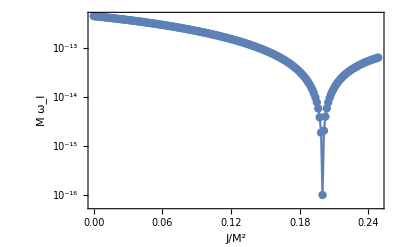

```mathematica
TI=Table[{TT[[i]][[1]],Im[TT[[i]][[2]]]},{i,1,Length[TT]}];
TR=Table[{TT[[i]][[1]],Re[TT[[i]][[2]]]},{i,1,Length[TT]}];
pn=ListLogPlot[Abs[TI],Frame->True,Joined->True,Mesh->All,FrameLabel->{"J/M^2","M ω_I"},PlotRange->All];
p2=Show[pn]
```

# Now the Polar Sector linearized

```mathematica
Q[l+1,m]:=0
Q[l,m]:=0
```

```mathematica
1-(2M r)/(r^2())
```

```mathematica
F[r]
```

1-(2 M)/r

```mathematica
ruleTortoise={rs'[r]-> ((r^2+a^2)/(r^2-2 M r+a^2)),rs''[r]-> D[((r^2+a^2)/(r^2-2 M r+a^2)),r]};
```

```mathematica
tort12={u2'[r]-> F[r]^-1 u2'[r]};(*tortoise coordinates*)
tort22={u2''[r]-> -F[r]^-2 F'[r]u2'[r]+F[r]^-2 u2''[r]};

tort13={u3'[r]-> F[r]^-1 u3'[r]};(*tortoise coordinates*)
tort23={u3''[r]-> -F[r]^-2 F'[r]u3'[r]+F[r]^-2 u3''[r]};
```

```mathematica
FFr[r_]=((r^2+a^2-2M r)/(r^2+a^2))^-1;
```

```mathematica
tort1Kerr={u2'[r]->FFr[r]^-1 u2'[r]}//Simplify;
tort2Kerr={u2'[r]->-FFr[r]^-2 FFr'[r]u2'[r]+FFr[r]^-2 u2''[r]}//Simplify;
tort1Kerr3={u3'[r]->FFr[r]^-1 u3'[r]}//Simplify
tort2Kerr3={u3'[r]->-FFr[r]^-2 FFr'[r]u3'[r]+FFr[r]^-2 u3''[r]}//Simplify
```

{u3'(r)→((a^2+r (r-2 M)) u3'(r))/(a^2+r^2)}

{u3'(r)→(2 M (r^2-a^2) u3'(r)+(a^2+r (r-2 M))^2 u3''(r))/((a^2+r^2)^2)}

```mathematica
LinearizedRadial=FullSimplify[ProjRadial/(I/r^(11/2) Exp[-I ω t](1/(r-2M))^(5/2)),{a≥0,l≥ 0,M>0}][[1]]
Speak["Finito, cazzone"];
LinearizedTheta=FullSimplify[ProjTheta(I r^(9/2)(2M-r)^3(1/(r-2M))^(3/2))/( Exp[-I ω t]),{a≥0,l≥ 0,M>0}][[1]]
Speak["Finito, cazzone"];
```

-1/(l (l+1))(l (l+1) u2(r) (2 a m M (2 M^2-3 M r-2 r^4 ω^2+r^2)-l (l+1) r^4 ω (r-2 M)+r^6 ω (2 M-r) ω_p^2+r^7 ω^3)-(2 M-r) (u3'(r) (2 a m M (-2 M^2+2 M r+r^4 ω^2)+l (l+1) r^4 ω (r-2 M))+2 a l (l+1) m M r (M-r) u2'(r)+2 a m M r (2 M^2-3 M r+r^2) u3''(r))+2 a m M r^3 ω^2 (r-M) u3(r))

1/(l (l+1) (r-2 M)^2)2 a m M (2 M-r) ((2 M-r) ((2 M-r) ((l (l+1) r-(l^2+l+4) M) u3'(r)+2 r (2 M-r) u3''(r))-(l^2+l-2) r^3 ω^2 u3(r)+l (l+1) r (4 M+r^3 ω^2-2 r) u2'(r))-l (l+1) u2(r) ((2 M-r) ((l^2+l+4) M-(l^2+l+2) r)+3 r^3 ω^2 (M-r)))+r^3 ω (u3(r) (ω (2 a m M-r^3 ω)+r^2 (r-2 M) ω_p^2)+(r-2 M) (l (l+1) r u2'(r)-r (r-2 M) u3''(r)-2 M u3'(r))+l (l+1) (2 M-r) u2(r))

```mathematica
uu2=Solve[LinearizedRadial==0,u2'[r]][[1]];
e3=LinearizedTheta/.uu2//Simplify;
u2final=Solve[e3==0,u2[r]]//FullSimplify
```

{{u2(r)→(1/(a m M (M-r))(u3'(r) (4 a^2 m^2 M^2 (l (l+1) (M-r)^2 (2 M-r)-2 r^3 ω^2 (M^2-3 M r+r^2)+r^7 ω^4)-4 a l (l+1) m M r^4 ω (2 M-r) (2 M+r^3 ω^2-r)+l^2 (l+1)^2 r^7 ω^2 (r-2 M)^2)+4 a^2 m^2 M^2 r^4 ω^2 (2 M^2-3 M r+r^2) u3''(r))+(2 r^5 ω u3(r) (2 a m M r ω^3+l (l+1) (r-2 M)^2 ω_p^2))/(2 M-r))/(2 l (l+1) (2 a m M (-(l^2+l+4) M+(l^2+l+2) r+(3 r^3 ω^2 (r-M))/(2 M-r))+((4 M+r^3 ω^2-2 r) (2 a m M (2 M^2-3 M r-2 r^4 ω^2+r^2)-l (l+1) r^4 ω (r-2 M)+r^6 ω (2 M-r) ω_p^2+r^7 ω^3))/(2 M^2-3 M r+r^2)+(l (l+1) r^7 ω^2 (4 a m M ω-l (l+1) (2 M-r)+r^2 (r-2 M) ω_p^2+r^3 (-ω^2)))/(2 a m M (M-r))))}}

```mathematica
Regola2=Join[u2final, D[u2final,r]];
```

```mathematica
Series[ProjTheta/.Regola2,{a,0,1}]
```

$Aborted